## Coupled Torsion Pendula

## Completed in class, March 18, 2025

This is the twelfth notebook for you to complete. It bears strong similarity to our eighth notebook (Coupled Harmonic Oscillators).

### Sign-Posting

We are working our way up to torsion waves. In the last notebook, you had one torsion rod with a wire exerting torque on each side of it. In this notebook, you are going to do two torsion rods and there will be a total of three wires exerting torque on the two rods.

Here is what we are working our way up to:
-Graphics-
This apparatus has 72 torsion rods. In the next class we will make a notebook that simulates an an apparatus with any number of rods, from 1 to 1000s, or whatever you like.

### Two Torques and Two Angular Accelerations

α_1=-ω_0^2 θ_1+ω_12^2(θ_2-θ_1)
 
α_2=-ω_0^2 θ_2-ω_12^2(θ_2-θ_1)
 
where,
 
ω_0^2≡κ/I

ω_12^2≡κ_12/I

### Coupled Torsion Pendula — Implementing the Angular Accelerations

```mathematica
omega0=2 Pi;
omega12=2Pi; (* we could make the middle wire weaker, but I have given it the same stiffness *)

α1[θ1_,θ2_]:=-omega0^2 θ1+omega12^2(θ2-θ1);
α2[θ1_,θ2_]:=-omega0^2 θ2-omega12^2(θ2-θ1);
```

### Graphics

Below is the completed graphics implementation from the last notebook. You need it to modify it to have two rods and three wires. Space the rods equally across the cuboid. In other words the centers of the rods should be at {-halfWidth/3,0,0} and {halfWidth/3,0,0}. There are going to be two angles. The angle of the left rod and the angle of the right rod.

```mathematica
halfHeight=1;
halfDepth=1;
halfWidth=5;
region={FaceForm[{Blue,Opacity[0.02]}],Cuboid[{-halfWidth,-halfDepth,-halfHeight},{halfWidth,halfDepth,halfHeight}]};
leftWire={Red,Line[{{-halfWidth,0,0},{-halfWidth/3,0,0}}]};
middleWire={Yellow,Line[{{-halfWidth/3,0,0},{halfWidth/3,0,0}}]};
rightWire={Green,Line[{{halfWidth/3,0,0},{halfWidth,0,0}}]};
coupledTorsionRodsGraphic[angle1_,angle2_]:=Graphics3D[{
region,
leftWire,
middleWire,
rightWire,
{Black, Thick,Line[{{-halfWidth/3,-halfDepth Cos[angle1],halfHeight Sin[angle1]},{-halfWidth/3,halfDepth Cos[angle1],-halfHeight Sin[angle1]}}]},
{Black, Thick,Line[{{halfWidth/3,-halfDepth Cos[angle2],halfHeight Sin[angle2]},{halfWidth/3,halfDepth Cos[angle2],-halfHeight Sin[angle2]}}]}
}]
coupledTorsionRodsGraphic[20°, -30°]
```

-Graphics3D-

### Simulation Parameters

```mathematica
tInitial = 0.0;
numberOfPeriods = 10;
period = 2Pi/omega0; 
tFinal = numberOfPeriods period; 
steps =1000 numberOfPeriods;
deltaT = (tFinal - tInitial)/steps;
```

### Initial Angles and Angular Velocities

Let’s let have both torsion pendula be initially held still at 20° and released:

```mathematica
tInitial=0.0;
theta1Initial=20 °;
omega1Initial=0;
theta2Initial=-20 °;
omega2Initial=0;
initialConditions={tInitial,theta1Initial,omega1Initial, theta2Initial,omega2Initial};
```

### Second-Order Runge-Kutta — Theory

t^*=t+Δt/2

θ_1^*=θ_1(t_i)+ω_1(t_i)·Δt/2

θ_2^*=θ_2(t_i)+ω_2(t_i)·Δt/2

t_(i+1)=t_i+Δt

ω_1(t_(i+1))=ω_1(t_i)+α_1(θ_1^*,θ_2^*)·Δt

ω_2(t_(i+1))=ω_2(t_i)+α_2(θ_1^*,θ_2^*)·Δt

θ_1(t_(i+1))=θ_1(t_i)+ (ω_1(t_i)+ω_1(t_(i+1)))Δt/2

θ_2(t_(i+1))=θ_2(t_i)+ (ω_2(t_i)+ω_2(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

Lots for you to finish.

```mathematica
rungeKutta2[cc_]:=(
(* Extract time, angle, and angular velocity from the list *)
curTime=cc[[1]];
curTheta1=cc[[2]];
curOmega1=cc[[3]];
curTheta2=cc[[4]];
curOmega2=cc[[5]];
(* Compute tStar, and theta1Star and theta2Star *)
tStar= curTime+deltaT/2;
theta1Star=curTheta1+curOmega1 deltaT/2;
theta2Star=curTheta2+curOmega2 deltaT/2;
(* Compute newTime, newTheta1, newTheta1, newOmega1, and newOmega2 *)
newTime=curTime+deltaT;
newOmega1=curOmega1+α1[theta1Star,theta2Star]deltaT;
newOmega2=curOmega2+α2[theta1Star,theta2Star]deltaT;
newTheta1=curTheta1+(curOmega1+newOmega1)deltaT/2;
newTheta2=curTheta2+(curOmega2+newOmega2)deltaT/2;
{newTime, newTheta1, newOmega1,newTheta2, newOmega2}
)
N[rungeKutta2[{0.1,20°,0.3, 40°,0.5}]] (* Test the rungeKutta2 function you just completed. *)
(* The output just below should be: *)
```

{0.101,0.349366,0.299998,0.698611,0.458644}

#### Displaying Oscillation as a Graph

Nest the procedure, transpose the results, and produce a plot of the angles, θ_1 and θ_2, as a function of time:

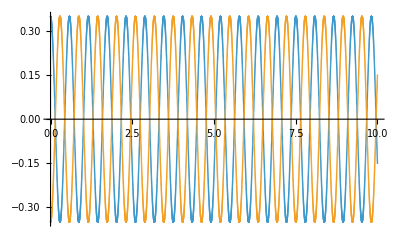

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
times = rk2ResultsTransposed[[1]];
θ1s = rk2ResultsTransposed[[2]];
θ2s = rk2ResultsTransposed[[4]];
θPlot = ListPlot[{Transpose[{times,θ1s}],Transpose[{times,θ2s}]}]
```

#### Animating the 3D Graphics

It’s also nice to have an animation, arranged so that the default duration of the animation is the actual duration of the animation:

```mathematica
Animate[coupledTorsionRodsGraphic[θ1s[[step]],θ2s[[step]]],{step, 0, steps, 1}, DefaultDuration->tFinal-tInitial]
```